```mathematica
Clear["Global`*"];
ClearSystemCache[];
SetDirectory[NotebookDirectory[]];
```

## Constants

```mathematica
Clear[mn];
mn=QuantityMagnitude[Quantity["NeutronMass"], "Gigaelectronvolts"/"SpeedOfLight"^2];
G =  6.67408*^-11; (*Grav Constant*)
hbarc = QuantityMagnitude[Quantity["ReducedPlanckConstant"]*Quantity["SpeedOfLight"], "Gigaelectronvolts"*"Femtometers" ]; (* in GeV fm *)
vs=230*^3;
vd=270*^3;
cspeed=QuantityMagnitude[Quantity["SpeedOfLight"], "Meters"/"Seconds"];
km=1000;
cm=1/100;
Gevto1fm=1000/197.3;
fm1to1m=10^15;
ρχ=0.4*^6; 
Prefactor=1;(*1/6.58*^-25;*) (* for d0 *)
ϵreg=10^(-4);
v=246;
cns=1;(*needs to be fixed*)
```

## Neutron Star EoS

#### Load in data

```mathematica
EoSHeaders = Import["eos_24_lowmass.dat"];
Dataset[EoSHeaders[[1,All]]] (*Print out headings so I know what I'm doing *)
EoSData =Drop[EoSHeaders, 1] ;(* Remove Headings *)
```

Dataset[<>]

Make Interpolating Functions

```mathematica
radius = EoSData[[All,1]];

rMin = radius[[1]];
rMax = Rstar= Last[radius];

μf[x_]:= Interpolation[ EoSData[[All, {1,8}]] ][x*Rstar]*1*^-3; (* Chemical potential in GeV *)

nb          = EoSData[[All,3]];
Yn          = EoSData[[All, 7]];
muList = EoSData[[All, 8]];

ndList = nb*Yn;
nprof=Interpolation[ Transpose[{radius,nb*Yn}]]; (* Neutron density in fm^-3*)

MNS = Interpolation[EoSData[[All, {1, 2}]]]; (* In units of M_⊙ *) 

p =Interpolation[EoSData[[All, {1, 12}]]]; (* in dyn/cm^2*)
```

```mathematica
(*EscVelSetUp[rad_?NumericQ] := Module[                                                           (* escape velocity inside star, in natural units *)
{GravPot,r}, 
GravPot =NIntegrate[(2.*G*MNS[r]*2.*^30)/(r^2*1.*^3), {r, rad, rMax}];
Sqrt[GravPot +(2.*G*MNS[rMax]*2.*^30)/(rMax*1.*^3)]/cspeed
]; 


ve = Interpolation[Table[{ri, EscVelSetUp[ri]}, {ri, rMin, Last[radius]}]];*)
```

```mathematica
(*Define Rstar, ζ0, B[r], nprof[r] (the true baryon density, NOT energy density) and μf[r].
Rstar in kmeters
nprof in the unit you want, I use fm^-3
ζ0 in the right unit to match nprof and nfree (That is in GeV^3)
μf in GeV
 IMPORTANT: definitions have to be functions that can be evaluated fast!*)
```

```mathematica
rtA[r_]:=Sqrt[1/(1 -(2*G*MNS[r*Rstar]*2*^30)/(r*Rstar*1*^3*cspeed^2))];
```

```mathematica
Clear[B];
B =NDSolveValue[{y'[x]==(2*G*(Rstar*1*^3))/(cspeed^2*(x*(Rstar*1*^3))^2)*((MNS[x*Rstar]*2*^30+p[x*Rstar]*0.1*(x*(Rstar*1*^3))^3/cspeed^2)/( 1 - (2*G*MNS[x*Rstar]*2*^30)/(cspeed^2*(x*(Rstar*1*^3)))))*y[x], y[1]==(1 - (2*G*MNS[1*Rstar]*2*^30)/(cspeed^2*(Rstar*1*^3)))},y, {x, rMin/Rstar, 1}];
(*takes as input r/Rstar (from 0 to 1)*)
```

```mathematica
ζ0=5.278368626202642(*Note that is not a problem that it is >1, as I use different units for ntrue and nfree, in same units result is 0.04*);
```

```mathematica
BTab = Table[{x, B[x/Rstar]}, {x, 0, Rstar, 0.01}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Export["B_data.dat", BTab, "Table"]
```

B_data.dat

```mathematica
NIntegrate[μf[x]x^2, {x, 0,11.643/Rstar}]/NIntegrate[x^2, {x, 0,11.643/Rstar}]
```

0.0859442

```mathematica
densityList = Table[{x, MNS'[x]*2*^30*1000/(4π x^2*(100000)^3)}, {x, rMin, 1.3, 0.01}];
Export["NSdens.dat", densityList, "Table"]
```

NSdens.dat

```mathematica
rMin
```

0.0045726

```mathematica
%*1000
```

4.5726

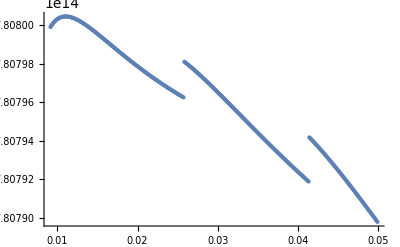

```mathematica
ListPlot[Table[{x, MNS'[x]*2*^30*1000/(4π x^2*(100000)^3)}, {x,2rMin,0.05, 0.0001}]]
```